```mathematica
SetDirectory[NotebookDirectory[]];
data = Association /@ Import["json/smokers_2015.json"];
```

```mathematica
data[[1]]
```

<|fips→15005,name→Kalawao, Hawaii,obesity→24,mortality→Null|>

```mathematica
points = {
	data[[All,"smoking"]],
	data[[All,"mortality"]]
};
```

```mathematica
Correlation@points
```

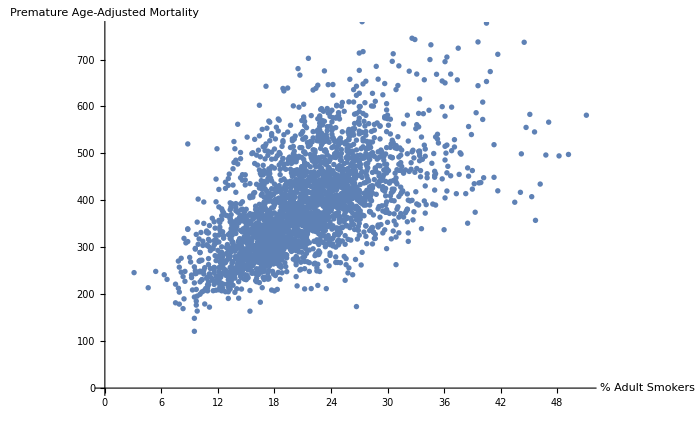

```mathematica
ListPlot[
	Transpose@points,
	AxesLabel->{"% Adult Smokers","Premature Age-Adjusted Mortality"},
	ImageSize->700
]
```

```mathematica
mortality = Select[data,#["mortality"]≠"Null"&];
```